```mathematica
IonDistribution[H_,KaList_]:=Reverse@Table[(H^i*(Times@@Drop[KaList,-i]))/Sum[H^i*(Times@@Drop[KaList,-i]),{i,0,Length[KaList]}],{i,0,Length[KaList]}];
(*Sample: IonDistribution[1,{0.8,10^-4}]*)
```

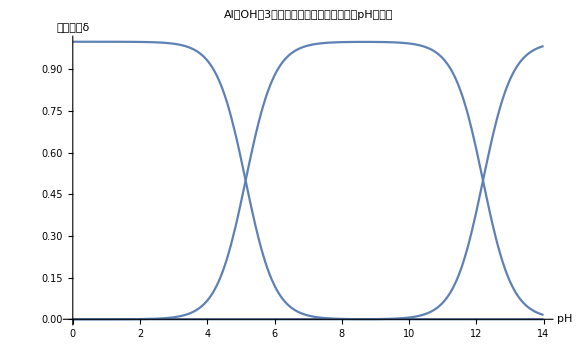

```mathematica
Plot[IonDistribution[10^-x,{10^-14/10^-8.86,10^-12.2}],{x,0,14},AxesLabel->{"pH","分布系数δ"},PlotLabel->Style["Al（OH）3及其共轭酸碱对的分布系数随pH变化图",Black,20],ImageSize->Large]
```

```mathematica
-#2&@@Log10[x/.Solve[D[#2&@@IonDistribution[x,{10^-14/10^-8.86,10^-12.2}],x]==0,x]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

8.67